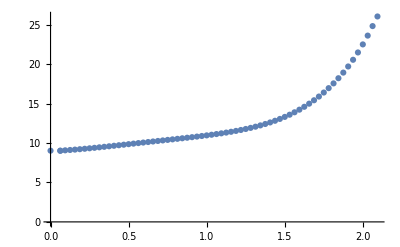

```mathematica
c4={{0,9.030202},{0.062500,9.023398},{0.062500,9.023398},{0.093750,9.074417},{0.125000,9.118160},{0.156250,9.165339},{0.187500,9.216783},{0.218750,9.272075},{0.250000,9.330591},{0.281250,9.391725},{0.312500,9.454933},{0.343750,9.519743},{0.375000,9.585755},{0.406250,9.652627},{0.437500,9.720076},{0.468750,9.787870},{0.500000,9.855822},{0.531250,9.923789},{0.562500,9.991668},{0.593750,10.059396},{0.625000,10.126949},{0.656250,10.194341},{0.687500,10.261621},{0.718750,10.328881},{0.750000,10.396251},{0.781250,10.463900},{0.812500,10.532042},{0.843750,10.600936},{0.875000,10.670886},{0.906250,10.742246},{0.937500,10.815424},{0.968750,10.890882},{1.000000,10.969142},{1.031250,11.050787},{1.062500,11.136467},{1.093750,11.226902},{1.125000,11.322884},{1.156250,11.425283},{1.187500,11.535051},{1.218750,11.653223},{1.250000,11.780922},{1.281250,11.919362},{1.312500,12.069848},{1.343750,12.233782},{1.375000,12.412661},{1.406250,12.608079},{1.437500,12.821724},{1.468750,13.055382},{1.500000,13.310935},{1.531250,13.590356},{1.562500,13.895715},{1.593750,14.229180},{1.625000,14.593022},{1.656250,14.989630},{1.687500,15.421534},{1.718750,15.891445},{1.750000,16.402307},{1.781250,16.957392},{1.812500,17.560416},{1.843750,18.215719},{1.875000,18.928487},{1.906250,19.705043},{1.937500,20.553159},{1.968750,21.482232},{2.000000,22.502269},{2.031250,23.618589},{2.062500,24.825489},{2.093750,26.045909}};
ListPlot[c4]
```

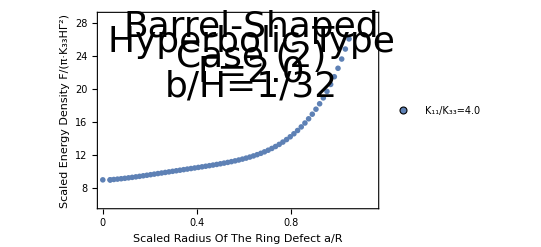

```mathematica
bb4=c4*Table[{0.5,1},{i,0,67}];
ListPlot[{bb4},PlotStyle->PointSize[0.01], Frame->{True, True, True, True}, FrameTicks->{{{8,12,16,20,24,28},None},{{0,0.2, 0.4, 0.6, 0.8,1},None}}, PlotRange->{{0,1.15},{6,28.8}},FrameLabel->{{"Scaled Energy Density F/(π·K_33HΓ^2)", None},{"Scaled Radius Of The Ring Defect a/R", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,36],PlotLegends->Placed[PointLegend[{"K_11/K_33=4.0"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Left, Top}],Epilog->{Text[Style["Barrel-Shaped",Directive[Black,36]],{0.63,27.5}],Text[Style["Hyperbolic Type",Directive[Black,36]],{0.63,25.7}],Text[Style["Case (2)",Directive[Black,36]],{0.63,23.9}],Text[Style["Γ=2.0",Directive[Black,36]],{0.63,22.1}],Text[Style["b/H=1/32",Directive[Black,36]],{0.63,20.3}]}]
```